## Sample Power Curve

```mathematica
SetDirectory["~/Dropbox/Notes/StatisticsEconometrics/MathematicalStatistics"];
```

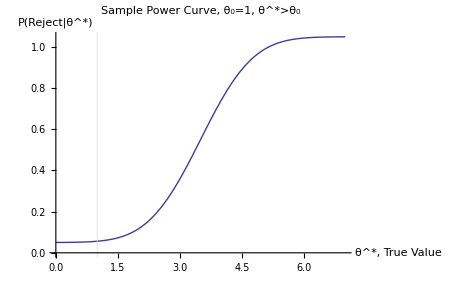

```mathematica
Show[Plot[CDF[NormalDistribution[3.5,1],t]+0.05,{t,0,7}],GridLines->{{1},{}},PlotLabel->"Sample Power Curve, θ_0=1, θ^*>θ_0",AxesLabel->{"θ^*, True Value","P(Reject|θ^*)"}]
```

```mathematica
Export["SamplePowerCurve.pdf",%,"PDF"]
```

SamplePowerCurve.pdf